```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Definition of R in terms of N=Log[a] *)
Ra[Nn_]:=6(2 H[Nn]^2+H[Nn] H'[Nn])
(* Definition of the f(R) Lagrangian  *)
f[R_]:=R-2Λ (1-1/(1+(R /(b Λ))^n))/.Λ->3(1-om-or)H0^2
n=1;
```

```mathematica
(* Definition of the ODE in terms of N=Log[a]=-Log[1+z] *)
ODE=-f'[R]H[Nn]^2+HL[Nn]^2-H0^2(1-om-or)+0(om Exp[-3 Nn]+or Exp[-4 Nn])+1/6(f'[R]R-f[R])-f''[R]H[Nn]^2 Ra'[Nn]/.R->Ra[Nn]//Simplify;
```

```mathematica
HL[Nn_]:=H0 Sqrt[om Exp[-3 Nn]+or Exp[-4 Nn]+(1-om-or)]
```

```mathematica
(* Solve the ODE *)
h=0.7348;
or0=0;
om0=.24;
H0=1;
modfried[om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=(modfried[om1,b1,Ns]=NDSolve[{(ODE/.om->om1/.b->b1/.or->or0//Evaluate)==0,H[Ns]==√(om0 Exp[-3 Ns]+or0 Exp[-4 Ns]+1-om0-or0),H'[Ns]==-(ⅇ^(-4 Ns) (3 ⅇ^Ns om0+4 or0))/(2 √(1+(-1+ⅇ^(-3 Ns)) om0+(-1+ⅇ^(-4 Ns)) or0))},H,{Nn,Ns,0},MaxSteps->2000000])
Hsol[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=(H[Nn]/.modfried[om1,b1,Ns][[1]])
Hsolp[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=(H'[Nn]/.modfried[om1,b1,Ns][[1]])
yH[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=((H[Nn]^2/om0-Exp[-3Nn]-or0/om0 Exp[-4Nn])/.modfried[om1,b1,Ns][[1]])
yHp[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=((3 ⅇ^(-3 Nn)+(4 ⅇ^(-4 Nn) or0)/om0+(2 H[Nn] H'[Nn])/om0)/.modfried[om1,b1,Ns][[1]])
```

```mathematica
Ns=Log[1/(1+30.)];
```

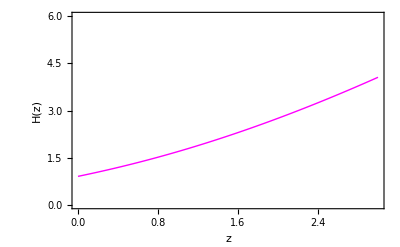

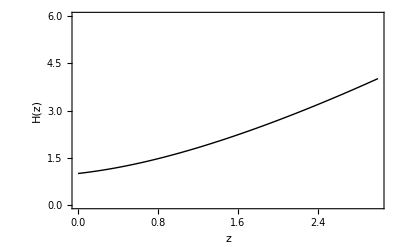

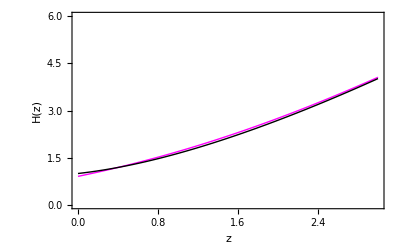

```mathematica
p1=Plot[Hsol[Log[1/(1+z)],om0,2,Ns],{z,0.,3.},PlotRange->{0,6},Frame->True,FrameLabel->{"z","H(z)"},PlotStyle->Magenta]
p2=Plot[Hsol[Log[1/(1+z)],om0,0.01,Ns],{z,0.,3.},PlotRange->{0,6},Frame->True,FrameLabel->{"z","H(z)"},PlotStyle->Black]
Show[p1,p2]
```

```mathematica
-Graphics-
lala=Table[{z,Hsol[Log[1/(1+z)],om0,0.5,Ns]},{z,Range[0,3,0.1]}]

(*Grid[lala]*)
Export["mfile_ODE_0.5.csv",lala,"CSV"]
```

-Graphics-

{{0.,0.960002},{0.1,1.01008},{0.2,1.0654},{0.3,1.1256},{0.4,1.19038},{0.5,1.25949},{0.6,1.33271},{0.7,1.40987},{0.8,1.49081},{0.9,1.57539},{1.,1.66347},{1.1,1.75495},{1.2,1.84971},{1.3,1.94767},{1.4,2.04873},{1.5,2.1528},{1.6,2.2598},{1.7,2.36967},{1.8,2.48231},{1.9,2.59768},{2.,2.71569},{2.1,2.83629},{2.2,2.95942},{2.3,3.08502},{2.4,3.21304},{2.5,3.34342},{2.6,3.47612},{2.7,3.61108},{2.8,3.74826},{2.9,3.88762},{3.,4.02911}}

mfile_ODE_0.5.csv